```mathematica
l:=0.3;
```

```mathematica
alpha := 20.0;
```

```mathematica
vel:=0.1;
```

```mathematica
A:={0.0,0.0};
```

```mathematica
T:={0.0,l};
```

```mathematica
sina:=Sin[alpha*Degree];
```

```mathematica
phi[t_]:=-t*vel*sina/l;
```

```mathematica
XO[t_]:=l*Cot[alpha*Degree]*Sin[phi[t]];
```

```mathematica
YO[t_]:=l*Cot[alpha*Degree]*Cos[phi[t]];
```

```mathematica
XA[t_]:=l*Sin[-phi[t]]+XO[t];
```

```mathematica
YA[t_]:=l*Cos[-phi[t]]+YO[t];
```

```mathematica
XO[0]
```

0

```mathematica
YO[0]
```

0.824243

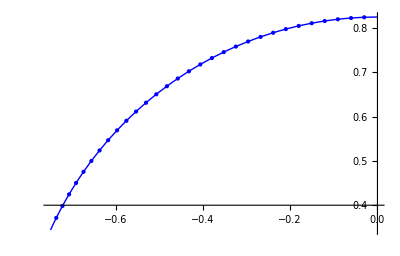

```mathematica
ParametricPlot[{XO[t],YO[t]},{t,0,10},Mesh->30,PlotStyle->{Red,Blue}]
```